```mathematica
ClearAll["Global`*"]
```

```mathematica
starvation =  ts*-Bm/(Em*Log[1-f0*M^(γ-1)])
recovery = ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])
```

-(Bm ts)/(Em Log[1-f0 M^(-1+γ)])

-(Bm ts (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η)]))

```mathematica
starvation
```

-(Bm ts)/(Em Log[1-f0 M^(-1+γ)])

```mathematica
recovery
```

-(Bm ts (-1+η))/(Em (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) M (1-f0 M^(-1+γ)))^(1-η)]))

```mathematica
Ratio = FullSimplify[starvation/recovery]
```

(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)])

```mathematica
RatioAnalytic = Ratio/.{
η->3/4,
γ->1.19,
f0->0.0202,
B0->1.9*10^(-2),
Bm->0.0245
}
```

-(4 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/Log[1-0.0202 M^0.19]

```mathematica
RatioAnalytic/.{M->0.36784590002898243}
```

6049.36+0. ⅈ

```mathematica
FullSimplify[D[(Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)])/((-1+η) Log[1-f0 M^(-1+γ)]),M]]
```

1/(Log[1-f0 M^(-1+γ)]^2)((1/(-M+(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) M)^η)+(M-f0 M^γ γ)/(M (M-f0 M^γ-(B0/Bm)^(1/(1-η)) ((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^η))) Log[1-f0 M^(-1+γ)]-(f0 M^(-1+γ) (-1+γ) (Log[1-((B0/Bm)^(1/(-1+η)) M)^(1-η)]-Log[1-((B0/Bm)^(1/(-1+η)) (M-f0 M^γ))^(1-η)]))/((-M+f0 M^γ) (-1+η)))

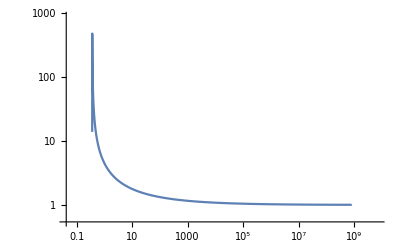

```mathematica
LogLogPlot[Re[RatioAnalytic],{M,0.01,10^20},PlotRange->All]
```

```mathematica
FindMaximum[Re[RatioAnalytic],M]
FindMinimum[Re[RatioAnalytic],M]
```

FindMaximum::sdprec: Line search unable to find a sufficient increase in the function value with MachinePrecision digit precision.

{6049.36,{M→0.367846}}

FindMinimum::sdprec: Line search unable to find a sufficient decrease in the function value with MachinePrecision digit precision.

{1.00715,{M→4.92266×10^8}}

```mathematica
Re[RatioAnalytic]/.M->10^10
```

-6.79748

```mathematica
DRatioAnalytic = D[RatioAnalytic,M]
DDRatioAnalyic = D[DRatioAnalytic,M]
```

-(4 (-0.322368/((1-1.28947 M^(1/4)) M^(3/4))+(0.322368 (1-0.024038 M^0.19))/((M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))))/Log[1-0.0202 M^0.19]-(0.015352 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19) M^0.81 Log[1-0.0202 M^0.19]^2)

-(0.030704 (-0.322368/((1-1.28947 M^(1/4)) M^(3/4))+(0.322368 (1-0.024038 M^0.19))/((M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))))/((1-0.0202 M^0.19) M^0.81 Log[1-0.0202 M^0.19]^2)-1/Log[1-0.0202 M^0.19]4 (0.241776/((1-1.28947 M^(1/4)) M^(7/4))-0.103921/((1-1.28947 M^(1/4))^2 M^(3/2))+(0.103921 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(3/2) (1-1.28947 (M-0.0202 M^1.19)^(1/4))^2)-(0.241776 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(7/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))-0.00147233/(M^0.81 (M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4))))-(0.000117842 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^3)+(0.0124351 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19) M^1.81 Log[1-0.0202 M^0.19]^2)-(0.000058921 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^2)

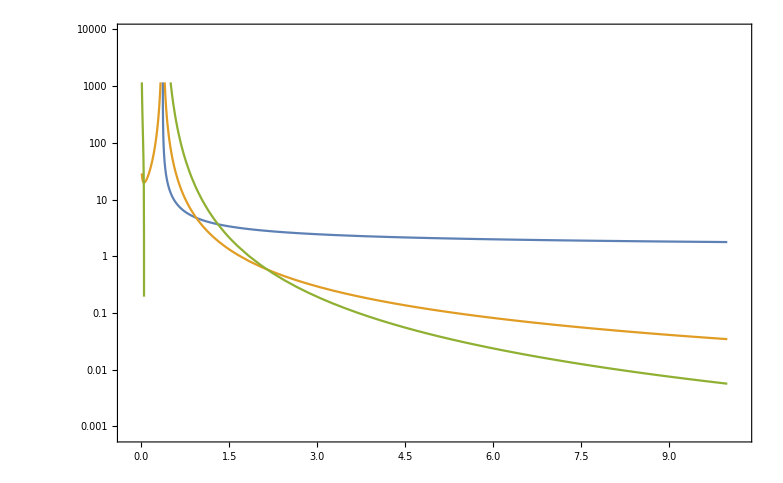

```mathematica
LogPlot[{RatioAnalytic,Abs[DRatioAnalytic],DDRatioAnalyic},{M,.01,10},Frame->True]
```

```mathematica
FullSimplify[DDRatioAnalyic]
```

$Aborted

```mathematica
NSolve[DDRatioAnalyic == RatioAnalytic,M,Reals]
```

FactorSquareFree::lrgexp: Exponent is out of bounds for function FactorSquareFree.

PolynomialGCD::lrgexp: Exponent is out of bounds for function PolynomialGCD.

NSolve[-(0.030704 (-0.322368/((1-1.28947 M^(1/4)) M^(3/4))+(0.322368 (1-0.024038 M^0.19))/((M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))))/((1-0.0202 M^0.19) M^0.81 Log[1-0.0202 M^0.19]^2)-1/Log[1-0.0202 M^0.19]4 (0.241776/((1-1.28947 M^(1/4)) M^(7/4))-0.103921/((1-1.28947 M^(1/4))^2 M^(3/2))+(0.103921 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(3/2) (1-1.28947 (M-0.0202 M^1.19)^(1/4))^2)-(0.241776 (1-0.024038 M^0.19)^2)/((M-0.0202 M^1.19)^(7/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4)))-0.00147233/(M^0.81 (M-0.0202 M^1.19)^(3/4) (1-1.28947 (M-0.0202 M^1.19)^(1/4))))-(0.000117842 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^3)+(0.0124351 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19) M^1.81 Log[1-0.0202 M^0.19]^2)-(0.000058921 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/((1-0.0202 M^0.19)^2 M^1.62 Log[1-0.0202 M^0.19]^2)==-(4 (Log[1-1.28947 M^(1/4)]-Log[1-1.28947 (M-0.0202 M^1.19)^(1/4)]))/Log[1-0.0202 M^0.19],M]

```mathematica
RatioSpecific=(
noise=0.2;
ParallelTable[
value=Re[Ratio/.{
M->i,
η->3/4,
γ->1.19,
f0->0.0202*(1+RandomReal[{-noise,noise}]),
B0->1.9*10^(-2)*(1+RandomReal[{-noise,noise}]),
Bm->0.0245*(1+RandomReal[{-noise,noise}])
}];
{i,value},
{i,0.1,10,0.00001}]
);
```

```mathematica
PosR=Select[RatioSpecific,#[[2]]>0&];
MAPosR=MovingAverage[PosR,100000];
```

```mathematica
AllometricAsymptotePlot=Show[{
ListLogPlot[PosR,Frame->True,PlotRange->{0,10},FrameLabel->{"Mass","σ/ρ"},PlotStyle->Directive[{Opacity[0.45]}]],
LogPlot[RatioAnalytic,{M,0.36784590002898243,10},PlotStyle->Black,PlotRange->All],
(*ListPlot[MAPosR,PlotStyle->Directive[{Dashed,ColorData[97,2]}]],*)
Graphics[{EdgeForm[Directive[Thick,ColorData[97,4]]],Directive[{Transparent}],Polygon[{{1.3,Log@0.05},{1.3,Log@9.95},{2.5,Log@9.95},{2.5,Log@0.05}}]}],
(*Graphics[{Dashed,Line[{{2.5,0},{2.5,10}}]}],*)
Graphics[Text[Style["Etruscan shrew",ColorData[97,4]],{3.75,Log@0.75}]],
Graphics[{Dashed,Black,Line[{{0.8029467083137317,Log@0.05},{0.8029467083137317,Log@9.95}}]}]
}]
```

-Graphics-

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_AlloAsymptote.jpg",AllometricAsymptotePlot,"JPG",ImageResolution->800]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_AlloAsymptote.jpg

```mathematica
starvation=-Bm/(Em*Log[1-f0*M^(γ-1)])
```

-Bm/(Em Log[1-f0 M^(-1+γ)])

```mathematica
growth= λ0*M^η2
```

M^η2 λ0

```mathematica
0.75-1
```

-0.25

```mathematica
-1/Log[1-M^-0.25]>M^-0.25
```

-1/Log[1-1/M^0.25]>1/M^0.25

```mathematica
Reduce[-1/Log[1-M^-0.25]>M^-0.25/.M->4]
```

True

```mathematica
1/M^0.25/.M->10
```

0.562341

Fixed points over mass

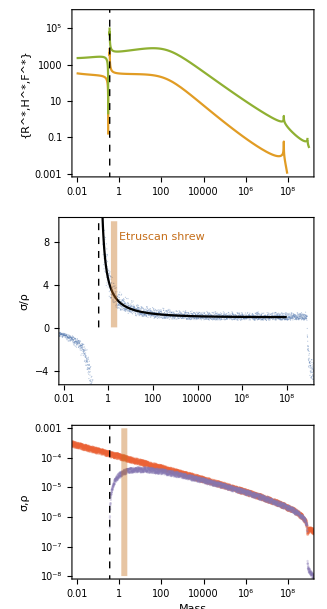

```mathematica
With[{
ts=1,
(*B0*)B0=1.9*10^(-2),
(*Bm*)Bm=0.0245,
(*Em*)Em=21.39/2*1000(*J/gram*),
(*η*)η=3/4,
(*η2*)η2=-0.206,
(*λ0*)λ0=3.3879*10^(-7),
(*ef*)ef=0.000001,
(*γ*)γ=1.19,
(*ζ*)ζ=1.01,
(*f0*)f0=0.0202,
(*mm0*)mm0=0.324},
Rstar = (μ (-λ+σ))/(λ ρ+μ σ);
Hstar = (α λ^2 (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ));
Fstar = (α λ μ (μ+ρ))/((β μ+λ ρ) (λ ρ+μ σ));
growth =N[ts* λ0*M^η2];
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])];
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])];
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])];
maintenance = ts*ef*B0*M^η;
resourcegrowth = ts*0.5;

Ratio = FullSimplify[starvation/recovery];
RatioSpecificAll=(
noise=0.2;
MassValues = RecurrenceTable[{Mass[n+1] == Mass[n]+1/100Mass[n],Mass[1]==0.0000001},Mass,{n,1,5000}];
ParallelTable[
sigmanoise=starvation*(1+RandomReal[{-noise,noise}])/.{M->i};
rhonoise = recovery*(1+RandomReal[{-noise,noise}])/.{M->i};
value=Re[sigmanoise/rhonoise];
{i,value,sigmanoise,rhonoise},
{i,MassValues}]
);
RatioSpecific = Transpose[{RatioSpecificAll[[All,1]],RatioSpecificAll[[All,2]]}];
SigmaSpecific = Transpose[{RatioSpecificAll[[All,1]],RatioSpecificAll[[All,3]]}];
RhoSpecific = Transpose[{RatioSpecificAll[[All,1]],RatioSpecificAll[[All,4]]}];
PosR=Select[RatioSpecific,#[[2]]>0 ||#[[2]]<=0  &];
(*MAPosR=MovingAverage[PosR,100000];*)
RstarM = Rstar/.{α->resourcegrowth,λ->growth,σ->starvation,ρ->recovery,β->maintenance,μ->mortality};
HstarM = Hstar/.{α->resourcegrowth,λ->growth,σ->starvation,ρ->recovery,β->maintenance,μ->mortality};
FstarM = Fstar/.{α->resourcegrowth,λ->growth,σ->starvation,ρ->recovery,β->maintenance,μ->mortality};
(*FAsymptote = FindMaximum[FstarM,M];*)
MassLimit=0.36784590002898243;
FPSigmaRhoPlot=GraphicsColumn[{
Show[{
LogLogPlot[{None,Re[HstarM],Re[FstarM]},{M,0.01,10^9},Frame->True,FrameLabel->{None,"{R^*,H^*,F^*}"},PlotRange->{{0.01,10^9},{0.001,All}},FrameTicks->{True,True},ImageSize->300],
Graphics[{Dashed,Black,Line[{{Log@MassLimit,-100},{Log@MassLimit,Log@10^10}}]}]
}(*,ImagePadding->{{43,14},{Automatic,Automatic}}*)],
Show[{
ListLogLinearPlot[Re[PosR],Frame->True,PlotRange->{{0.01,10^9},{-5,10}},FrameLabel->{None,"σ/ρ"},FrameTicks->{True,True},PlotStyle->Directive[{Opacity[0.45]}],ImageSize->300],
LogLinearPlot[Re[Ratio],{M,0.36784590002898243,10^8},PlotStyle->Black,PlotRange->All],
(*ListPlot[MAPosR,PlotStyle->Directive[{Dashed,ColorData[97,2]}]],*)
Graphics[{(*EdgeForm[Directive[Thick,ColorData[97,4]]],*)Directive[{ColorData[97,6],Opacity[0.4]}],Polygon[{{Log@1.3,0.05},{Log@1.3,9.95},{Log@2.5,9.95},{Log@2.5,0.05}}]}],
(*Graphics[{Dashed,Line[{{2.5,0},{2.5,10}}]}],*)
Graphics[Text[Style["Etruscan shrew",FontSize->Medium,ColorData[97,6]],{Log@250,8.5}]],
Graphics[{Dashed,Black,Line[{{Log@MassLimit,0.05},{Log@MassLimit,9.95}}]}]
}(*,ImagePadding->{{43,14},{Automatic,Automatic}}*)],
Show[{
ListLogLogPlot[Re[SigmaSpecific],PlotRange->{{0.01,10^9},{10^-8,10^-3}},Frame->True,FrameLabel->{"Mass","σ,ρ"},PlotStyle->Directive[{Opacity[0.3],ColorData[97,4]}],ImageSize->300],
ListLogLogPlot[Re[RhoSpecific],Frame->True,PlotStyle->Directive[{Opacity[0.3],ColorData[97,5]}]],
Graphics[{Dashed,Black,Line[{{Log@MassLimit,-100},{Log@MassLimit,Log@10^-3}}]}],
Graphics[{(*EdgeForm[Directive[Thick,ColorData[97,4]]],*)Directive[{ColorData[97,6],Opacity[0.4]}],Polygon[{{Log@1.3,Log@(10^-8)},{Log@1.3,Log@(10^-3)},{Log@2.5,Log@(10^-3)},{Log@2.5,Log@(10^-8)}}]}]
(*Graphics[{Dashed,Line[{{2.5,0},{2.5,10}}]}],*)
(*Graphics[Text[Style["Etruscan shrew",FontSize->Medium,ColorData[97,6]],{Log@40,Log@(10^-3.2)}]]*)
}(*,ImagePadding->{{43,0},{Automatic,Automatic}}*)]
}(*,ImagePadding->{{10,10},{200,110}}*)]
]
```

```mathematica
PosR
```

{{1.×10^-7,-0.0208283},{1.01×10^-7,-0.0180464},{1.0201×10^-7,-0.0195155},{1.0303×10^-7,-0.0200032},{1.0406×10^-7,-0.0255698},4991,{3.88672×10^14,-4.28223},{3.92559×10^14,-2.83717},{3.96484×10^14,-4.05111},{4.00449×10^14,-4.59829}}
 |  |  |  |

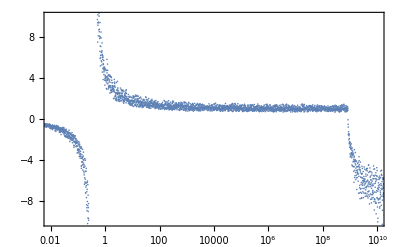

```mathematica
ListLogLinearPlot[Re[PosR],Frame->True,PlotRange->{{0.01,10^10},{-10,10}}]
```

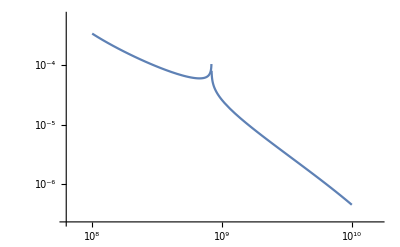

```mathematica
LogLogPlot[Re[FstarM],{M,10^8,10^10}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FPAllometric.pdf",FPSigmaRhoPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_FPAllometric.pdf

```mathematica
MassValues = RecurrenceTable[{Mass[n+1] == Mass[n]+1/100Mass[n],Mass[1]==0.0000001},Mass,{n,1,5000}];
```

```mathematica
Solve[(f0*M^(γ-1)==1)/.{f0->0.0202,γ->1.19},M]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{M→8.30239×10^8}}